```mathematica
Get["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\Mathematica\\CDTFunctions.wl"]
```

```mathematica
data = Import["C:\\Users\\jacks\\Documents\\GitHub\\cdt_rust\\data\\Statistical_Volume_64_TimeSize_8_stepsize_4_sample_123.csv"]
```

```mathematica
sorted = SortBy[data,-#[[2]]&];
```

```mathematica
sorted[[234]]
```

{102_77_79_71_45_19_7_2,0}

```mathematica
Mean[Table[N[Oscilatory[ToExpression@ StringSplit[sorted[[i,1]],"_"]]],{i,100}]]
```

8.36023

```mathematica
Mean[Table[N[Oscilatory[ToExpression@ StringSplit[sorted[[-i,1]],"_"]]],{i,100}]]
```

8.4767

```mathematica
Oscilatory[l_]:=Sqrt[Mean[Differences[l]^2]]
```

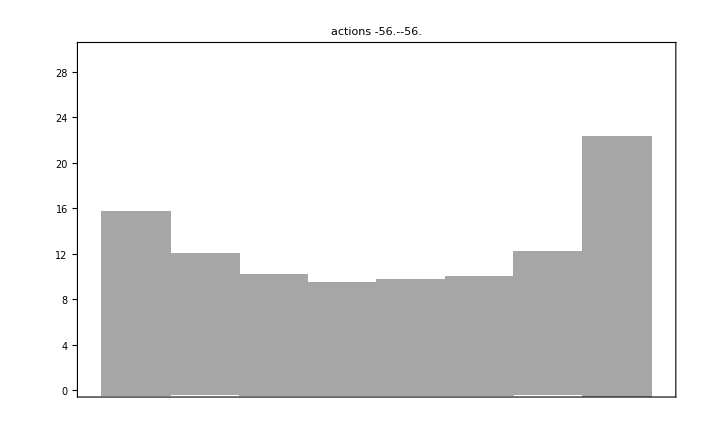

```mathematica
a = DistributionChart[Transpose[Table[N[ToExpression@ StringSplit[sorted[[-i,1]],"_"]],{i,10000}]],PlotRange->{0,30},ChartElementFunction->ChartElementData["Density"],ChartStyle-> {Directive[EdgeForm[None],Orange]},BarSpacing->0,PlotLabel-> "actions "<>ToString[sorted[[-1,2]]]<>"-"<>ToString[sorted[[-10000,2]]]]
```

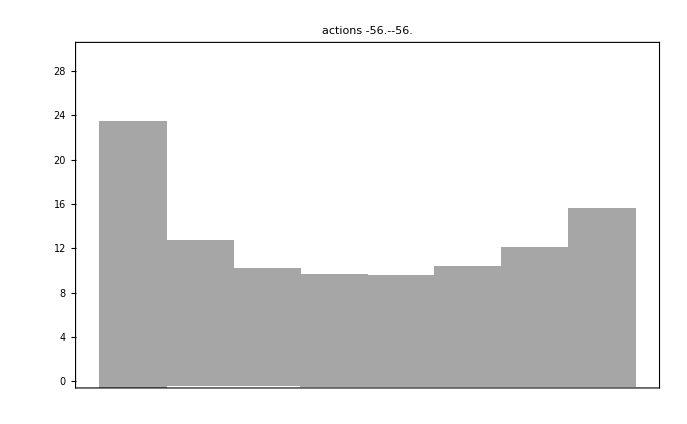

```mathematica
b = DistributionChart[Transpose[Table[N[ToExpression@ StringSplit[sorted[[i,1]],"_"]],{i,10000}]],PlotRange->{0,30},ChartElementFunction->ChartElementData["Density"], ChartStyle-> {Directive[EdgeForm[None],Blue]},BarSpacing->0,PlotLabel-> "actions "<>ToString[sorted[[1,2]]]<>"-"<>ToString[sorted[[10000,2]]]]
```